```mathematica
Needs["HierarchicalClustering`"]
Hex2RGB=RGBColor@@(IntegerDigits[#~StringDrop~1~FromDigits~16,256,3]/255.)&;
colors={
{{"white","#fffefc"},{"pearl","#fbfcf7"},{"alabaster","#fefaf0"},{"snow","#f4fefd"},{"ivory","#fef7e5"},{"cream","#fffbda"},{"eggshell","#fef9e3"},{"cotton","#fbfcf7"},{"chiffon","#fafaf1"},{"salt","#f8efec"},{"lace","#faf3ea"},{"coconut","#fff1e6"},{"linen","#f2ebd3"},{"bone","#e7dfcc"},{"porcelain","#fffffc"},{"parchment","#fcf6df"},{"rice","#fbf6ef"}},{{"blue","#0074d9"},{"navy","#001f3f"},{"aqua","#7fdbff"},{"sky","#00b2ff"},{"teal","#39cccc"},{"slate","#757b87"},{"indigo","#281e5d"},{"cobalt","#1438bd"},{"ocean","#026063"},{"peacock","#002d37"},{"azure","#1621a6"},{"cerulean","#0592c2"},{"lapis","#2632c2"},{"spruce","#2c3e4b"},{"stone","#59788d"},{"aegean","#1e456e"},{"berry","#24146f"},{"denim","#141e3c"},{"admiral","#060f94"},{"sapphire","#52b2c0"},{"arctic","#82edfe"}},
{{"tan","#e5dbac"},{"beige","#ecdc99"},{"macaroon","#f7df75"},{"hazelwood","#c9bc8e"},{"granola","#d6b75a"},{"oat","#dec98a"},{"eggnog","#fbe29d"},{"fawn","#c7a951"},{"sand","#d7b963"},{"sepia","#e3b678"},{"latte","#e9c17b"},{"oyster","#dcd69f"},{"biscotti","#e3c565"},{"parmesean","#fee993"},{"hazelnut","#bda55d"},{"sandcastle","#dbc27d"},{"buttermilk","#fdefb2"},{"sanddollar","#ebe7b9"},{"shortbread","#fce791"}},
{{"yellow","#FFDC00"},{"canary","#fac801"},{"gold","#f9a602"},{"daffodil","#feee88"},{"flaxen","#d5b65a"},{"butter","#fee226"},{"lemon","#effd5f"},{"mustard","#e9b829"},{"corn","#e4cd04"},{"medallion","#e4b103"},{"dandelion","#fdce2a"},{"bumblebee","#fce206"},{"banana","#fcf4a3"},{"butterscotch","#fabd04"},{"dijon","#c29200"},{"honey","#ec9707"},{"blonde","#fdeb75"},{"pineapple","#ffe327"},{"tuscansun","#fcd12a"}},
{{"orange","#ff851b"},{"tangerine","#f98228"},{"merigold","#fdae1d"},{"cider","#b66827"},{"rust","#8c4005"},{"ginger","#bc5703"},{"tiger","#fb6b02"},{"bronze","#b2560c"},{"cantaloupe","#fca172"},{"apricot","#ed810f"},{"carrot","#ed7116"},{"squash","#c95c09"},{"spice","#7a3a03"},{"marmalade","#d16102"},{"amber","#893201"},{"sandstone","#d57128"},{"yam","#cc5801"}},{{"red","#ff4136"},{"cherry","#9a0f02"},{"rose","#e2252a"},{"jam","#600f0b"},{"merlot","#541f1b"},{"garnet","#5f0a04"},{"crimson","#b8100a"},{"ruby","#900503"},{"scarlet","#910d08"},{"redwine","#4c0805"},{"redapple","#a91b0d"},{"mahogany","#420d09"},{"blood","#710c04"},{"sangria","#5f1914"},{"currant","#670c07"},{"blush","#bb544a"},{"candy","#d31603"},{"lipstick","#9b0f02"}},{{"pink","#f69acd"},{"fuchsia","#f012be"},{"punch","#f25278"},{"watermelon","#fe809c"},{"flamingo","#fda4b8"},{"rouge","#f26c8c"},{"salmon","#fdab9f"},{"coral","#fe7d67"},{"peach","#fb9483"},{"strawberry","#fc4c4e"},{"rosewood","#a04242"},{"lemonade","#fabacb"},{"taffy","#fa85c4"},{"bubblegum","#fd5ca8"},{"balletslipper","#f69abf"},{"crepe","#f1b7c6"},{"maroon","#85144be"},{"hotpink","#ff1696"}},{{"purple","#b10dc9"},{"mauve","#7a4a89"},{"violet","#710193"},{"boysenberry","#630536"},{"lavender","#e3a0f6"},{"maroon","#85144B"},{"plum","#601a36"},{"lilac","#b65fcd"},{"periwinkle","#be93d4"},{"eggplant","#311431"},{"iris","#9866c5"},{"heather","#9b7cb9"},{"amethyst","#a45de4"},{"raisin","#290916"},{"orchid","#af69ee"},{"mulberry","#4d0220"}},{{"green","#2ecc40"},{"chartreuse","#b0fc37"},{"juniper","#395311"},{"sage","#728c69"},{"lime","#01ff70"},{"fern","#5dbc64"},{"olive","#98bf64"},{"emerald","#038911"},{"pear","#74b62d"},{"moss","#476d1e"},{"shamrock","#03ac13"},{"seafoam","#3cec96"},{"pine","#24501e"},{"parakeet","#02c04a"},{"mint","#98ecc3"},{"seaweed","#354b21"},{"pickle","#5a7d36"},{"pistachio","#b2d3c1"},{"basil","#32622d"},{"crocodile","#5f7c3a"}},
{{"brown","#241709"},{"coffee","#4b371c"},{"mocha","#3c290d"},{"peanut","#795c34"},{"carob","#35260f"},{"hickory","#371d10"},{"pecan","#4a2512"},{"walnut","#432711"},{"caramel","#66360f"},{"gingerbread","#5d2c04"},{"chocolate","#2c1603"},{"tortilla","#9a7b4f"},{"umber","#352415"},{"tawny","#7e491d"},{"brunette","#391e07"},{"cinammon","#642b0d"},{"penny","#522915"}},{{"grey","#aaaaaa"},{"shadow","#373737"},{"graphite","#584d5b"},{"iron","#332d31"},{"pewter","#6a6880"},{"cloud","#c5c5d0"},{"silver","#dddddd"},{"smoke","#59515f"},{"anchor","#42424c"},{"ash","#554c4d"},{"porpoise","#4d4c5d"},{"dove","#7c6e7f"},{"fog","#655965"},{"flint","#7d7c9c"},{"pebble","#333333"},{"lead","#403f4e"},{"coin","#9897a9"},{"fossil","#787276"}},{{"black","#111111"},{"ebony","#080401"},{"crow","#3d3934"},{"charcoal","#222023"}}};
```

## Exploration of the Space

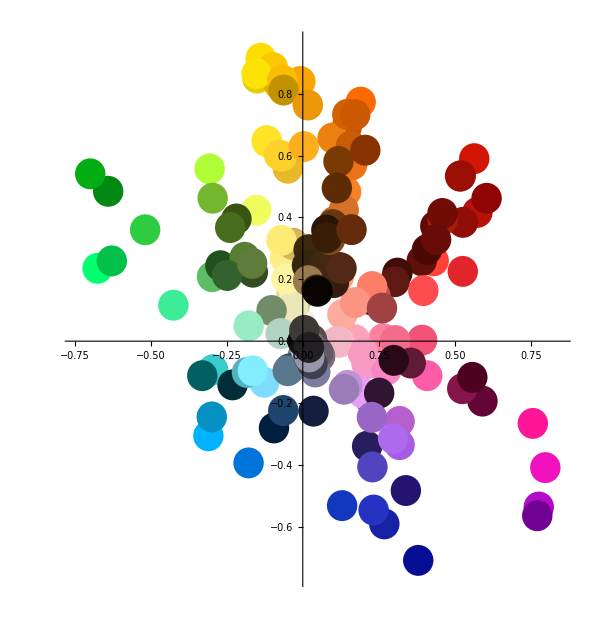

```mathematica
Show@@{(MapAt[Graphics[{#, Disk[ColorConvert[#,"LAB"][[{2,3}]],0.05]}]&@Hex2RGB[#]&,#,2]&/@#&/@colors)[[;;,;;,2]],Axes->True,AxesOrigin->{0,0} }
```

```mathematica
Length@Flatten[(MapAt[ColorConvert[#,"LAB"]&@Hex2RGB[#]&,#,2]&/@#&/@colors),1][[;;,2]]
```

204

```mathematica
Show@@{(MapAt[Graphics3D[{Glow[#],Black, Sphere[ColorConvert[#,"LUV"],0.03]}]&@Hex2RGB[#]&,#,2]&/@#&/@colors)[[;;,;;,2]],Axes->True,AxesOrigin->{0,0,0},AxesLabel->{"Lightness", "Red-Green","Blue-Yellow"}}
```

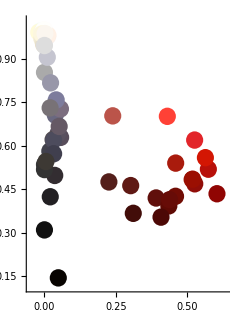

```mathematica
Show@@{(MapAt[Graphics[{#, Disk[ColorConvert[#,"LAB"][[{2,1}]],0.03]}]&@Hex2RGB[#]&,#,2]&/@#&/@colors)[[{1,6,-2,-1},;;,2]],Axes->True,AxesOrigin->{0,0} }
```

## Color Distance

```mathematica
Clear[DL,Sl,kl,DCab,kc,Sc,DHab,kh,Sh,C1,C2,cone,ctwo,e]
cdist94[{l1_,a1_,b1_},{l2_,a2_,b2_}]:=Evaluate@Function[{l1,a1,b1,l2,a2,b2},
Evaluate[#1/.#2/.#2/.#2&[(DL/kl/Sl)^2+(DCab /kc/Sc)^2+(DHab/kh/Sh)^2,
{DL->l1-l2,
DHab->Sqrt[(a1-a2)^2+(b1-b2)^2-DCab^2],
DCab->C1-C2,
C1->Sqrt[a1^2+b1^2],
C2->Sqrt[a2^2+b2^2],
Sl->1,
Sc->1+K1 C1,
Sh->1+K2 C1,
kl->1,
K1->0.045,
K2->0.015,
kc->1,
kh->1}]]
][l1,a1,b1,l2,a2,b2]

Clear[DLp, Lbar, Cbar, a1p, a2p, Cbarp, C1p,C2p,h1p,h2p]
```

## Clustering and Grouping

```mathematica
kruskal[pts_]:=Module[{n=Length[pts[[2]]],vpairs,jj=0,hh,pair,dist,c1,c2,c1c2},Do[hh[k]={k},{k,n}];
vpairs=Sort[Flatten[Table[{pts[[k,l]],{k,l}},{k,1,n-1},{l,k+1,n}],1]];
First[Last[Reap[While[jj<Length[vpairs],jj++;
{dist,pair}=vpairs[[jj]];
{c1,c2}={hh[pair[[1]]],hh[pair[[2]]]};
If[c1=!=c2,Sow[vpairs[[jj,2]]];
c1c2=Union[c1,c2];
Do[hh[c1c2[[k]]]=c1c2,{k,Length[c1c2]}];
If[Length[hh[pair[[1]]]]==n,Break[]];];]]]]];
```

```mathematica
With[{mat=#1,edges=kruskal@#1},System`Graph[
#[[1]]<->#[[2]]&/@ edges,
ImagePadding->10,GraphLayout->"SpringElectricalEmbedding",
System`VertexStyle->MapIndexed[#2[[1]]->Directive[Hex2RGB@#1]&,Flatten[colors,1][[;;,2]] ],
VertexSize->3,
System`EdgeWeight-> (Part@@Flatten[{{mat},#},1]&/@edges)
]]&[DistanceMatrix[#,DistanceFunction->cdist94]&@Flatten[(MapAt[ColorConvert[#,"LUV"]&@Hex2RGB[#]&,#,2]&/@#&/@colors),1][[;;,2]]]
```

-Graphics-

```mathematica
SizeSplit[size_]:=Flatten[#,1]&@CondClusterSplit[#,#[[4]]+#[[5]]>size&]&
CondClusterSplit[clist_,cond_]:=Map[If[And[Head@#===Cluster,cond@#],ClusterSplit[#,2],{#}]&,clist];
GeneralClusterFlatten[c_]:=If[Head@c===Cluster,ClusterFlatten@c,{c}];
GeneralClusterFlatten/@SizeSplit[10]@SizeSplit[10]@SizeSplit[15]@#&@(ClusterSplit[#,20]&@Agglomerate[Flatten[(MapAt[ColorConvert[#,"LUV"]&@Hex2RGB[#]&,#,2]&/@#&/@colors),1][[;;,2]]->Range[Length@Flatten[colors,1]] ,Linkage->"Ward" ])/.Dispatch@MapIndexed[#2[[1]]->Graphics[{Hex2RGB@#1[[2]],Disk[]},ImageSize->22]&,Flatten[colors,1]]//Map[TableForm,SortBy[#,Length]]&
```

{-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-}

```mathematica
Map[Graphics[{RGBColor@ColorConvert[#,"LAB"->"RGB"],Disk[]},ImageSize->30]&,#]&/@
(GeneralClusterFlatten/@
Flatten[CondClusterSplit[#,#[[4]]+#[[5]]>7&],1]&@
(ClusterSplit[#,20]&@
Agglomerate[
(ColorConvert[1-#&/@Hex2RGB@#[[2]],"LAB"]&/@Flatten[colors[[{3,4,5,6,7,8,10}]],1 ])
 ,Linkage->"Ward" ])) //Map[TableForm,SortBy[#,Length]]&
```

{-Graphics-,-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-}

```mathematica
BorderedOuter[f_,l1_,l2_]:=BorderedOuter[f,Identity,l1,l2]
BorderedOuter[f_,d_,l1_,l2_]:=Transpose[{Prepend[d/@l1,""]}~Join~Transpose[{d/@l2}~Join~Outer[f,l1,l2,1]]]
Graphics[{RGBColor@ColorConvert[#,"LAB"->"RGB"],Disk[]},ImageSize->30]&
```

```mathematica
MinDistElems[d_,l1_,l2_]:=Transpose[{d/@l1}~Join~Transpose[{d@Part[l2,Ordering[#1,1][[1]] ],Min@#1}&/@Outer[cdist94,l1,l2,1]]]//SortBy[#,-#[[3]]&]&

NMostDifferent[d_,initial_,n_]:=Module[{i,next={},closest=initial},
For[i=1,i≤n,i++,
AppendTo[next,{"","#"<>StringJoin[IntegerString[#,16,2]&@Round@#&/@(255*ColorConvert[#[[1,1]],"LUV"->"RGB"])]}&@closest];
closest = Map[With[{distance=d@@{#[[1]],closest[[1,1]]}},If[distance < #[[3]],{#[[1]],closest[[1,1]],distance},#]]&,closest[[2;;]]]//SortBy[#,-#[[3]]&]&;
];
Return[{next,closest}];
]
```

```mathematica
diffs=MinDistElems[Identity,
(*Graphics[{RGBColor@ColorConvert[#,"LUV"->"RGB"],Disk[]},ImageSize->100]&,*)
(ColorConvert[1-#&/@Hex2RGB@#[[2]],"LUV"]&/@Flatten[colors[[{3,4,5,6,7,8,10}]],1 ]),
ColorConvert[#,"LUV"]&/@Hex2RGB/@Flatten[colors[[;;,;;,2]],1]
];
```

```mathematica
Graphics[{Hex2RGB[#],Disk[]},ImageSize->70]&/@NMostDifferent[cdist94,diffs,12][[1,;;,2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graphics[{#,Disk[]},ImageSize->40]&/@(Hex2RGB/@Flatten[#,1]&@colors[[2,;;,2]]//SortBy[#,#[[3]]&] &)
Graphics[{#,Disk[]},ImageSize->40]&/@(Hex2RGB/@Flatten[#,1]&@colors[[9,;;,2]]//SortBy[#,#[[2]]&] &)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{u,w,v}=SingularValueDecomposition[
Transpose@With[{d=Mean/@Transpose@#},#-d&/@#]&@(ColorConvert[#,"LUV"]&/@Hex2RGB/@Flatten[colors[[;;,;;,2]],1])
]
```

{{{0.0945347,-0.312151,-0.945317},{0.370733,0.892308,-0.257573},{0.923916,-0.326111,0.200079}},{«1»},{{-0.029388,-0.0373354,-0.102352,-0.0933707,-0.0920707,-0.0936173,-0.0928031,-0.0936813,-0.0926923,«186»,-0.00745138,0.0776115,0.0588246,-0.0292825,0.000899837,0.152399,0.209517,0.0669032,0.111291},«202»,{-«21»,«202»,«19»}}}

```mathematica
Show[Graphics3D[Arrow[{{0,0,0},#}]]&/@Transpose@u,
Axes->True,AxesOrigin->{0,0,0},AxesLabel->{"L","A","B"}]
```